```mathematica
Guy F. Mongelli, F.E.
Prof. Lacks
```

```mathematica
Coulomb's constant
```

```mathematica
ke=8.9875517873681764*10^9; (* N*m^2/C^2 *)
```

```mathematica
Plotting the indicidual force field potentials for some of the atoms which will appear in poly-alkanes, polyethers and other expected materials.
```

```mathematica
Create a table for the list of opls-aa atom types in each polymer and the number of times they occur in a trimer
```

```mathematica
Create a table for the contants as a function of opls-aa atom type broken down into toplogy sections
```

```mathematica
TableForm[Table[,{k,4}],TableHeadings->{{"ϕ6","ϕ7","ϕ8","ϕ9"},{"k=.1","k=1","k=10","k=100"}}]
```

ϕ6 | coeffs[1.]
ϕ7 | coeffs[2.]
ϕ8 | coeffs[3.]
ϕ9 | coeffs[4.]

```mathematica
BONDS
```

```mathematica
The bonded parameters are determined by pairs of atom classes.  The OPLS atom types are grouped together by element and coordination number.  The bonds atom classes in the polyalkanes and poly - ethers are : CT HC, HO OH, CT OH, C O and OW HW.  The poly-silicones have their own custom section with constants for the literature.  There are inserted into a
```

```mathematica
Bonding potentials for each atom type have parameters kr and r0.
```

```mathematica
kr[CT HC]=462750.4;
```

```mathematica
r0[CT HC]=.109;
```

```mathematica
kr[HO OH]=462750.4;
```

```mathematica
r0[HO OH]=.0945;
```

```mathematica
kr[CT OH]=267776;
```

```mathematica
r0[CT OH]=.141;
```

```mathematica
kr[C O]=476976;
```

```mathematica
r0[C O]=.1229;
```

```mathematica
kr[OH HW]=502080;
```

```mathematica
r0[OH HW]=.09572;
```

```mathematica
Custom Si bonding
```

```mathematica
Plot[1*(r-6)^2+10,{r,0,10},PlotRange->{0,30},AxesLabel->{Style["r"|"θ",30],Style["E_Bond/E_Angle",25]},LabelStyle->Directive[0]]
```

```mathematica
ANGLES
```

```mathematica
Bonding potentials for each atom type have parameters kθ and θ0.
```

```mathematica
kθ[CT CT HC]=313.8;
```

```mathematica
θ0[CT CT HC]=110.7;
```

```mathematica
kθ[CT CT CT]=488.273;
```

```mathematica
θ0[CT CT CT]=112.7;
```

```mathematica
kθ[CT OS CT]=502.08;
```

```mathematica
θ0[CT OS CT]=109.5;
```

```mathematica
kθ[HC C OS]=334.72;
```

```mathematica
θ0[HC C OS]=115;
```

```mathematica
kθ[Si O Si]=
```

```mathematica
θ0[Si O Si]=
```

```mathematica
kθ[opls182]=
```

```mathematica
θ0[opls182]=
```

```mathematica
kθ[opls154]=
```

```mathematica
θ0[opls154]=
```

```mathematica
kθ[opls155]=
```

```mathematica
θ0[opls155]=
```

```mathematica
kθ[opls157]=
```

```mathematica
θ0[opls157]=
```

```mathematica
kθ[opls158]=
```

```mathematica
θ0[opls158]=
```

```mathematica
Custom Si angles
```

```mathematica
Plot[1*(r-6)^2+10,{r,0,10},PlotRange->{0,30},AxesLabel->{Style["r"|"θ",30],Style["E_Bond/E_Angle",25]},LabelStyle->Directive[0]]
```

```mathematica
DIHEDRALS
```

```mathematica
The dihedral interaction energies are determined by a function which has five constants or parameters determined by the combination of atomic classes.  The atomic sub-class for a particular OPLS atom type is given in the ffnonbonded.itp file.  The OPLS atom types are grouped by element and coordination number.
```

```mathematica
See p. 81 of the gromacs manual (ftp://ftp.gromacs.org/pub/manual/manual-4.6.4.pdf)
```

```mathematica
Erb[ϕ_]=∑_(n=1)^5 C[n]*(Cos[ϕ-(Pi/2)])^n
```

```mathematica
Bonding potentials for each atom type have parameters Cn and Cos[n*θ].
```

```mathematica
A test case of the example given on p. 81 of the manual is given:
```

```mathematica
Erbtest[ϕ_]=∑_(n=0)^5 Ct[n,0]*
(Cos[ϕ-(Pi)])^n
```

9.28-12.16 Cos[ϕ]-13.12 Cos[ϕ]^2+3.06 Cos[ϕ]^3+26.24 Cos[ϕ]^4+31.5 Cos[ϕ]^5

```mathematica
In the following lines the constant functions, C[n,s] correspond to the nth constant of a particular four atom class denoted 0.  These constants are in kJ/mol.
```

```mathematica
Ct[0,0]=9.28;
```

```mathematica
Ct[1,0]=12.16;
```

```mathematica
Ct[2,0]=-13.12;
```

```mathematica
Ct[3,0]=-3.06;
```

```mathematica
Ct[4,0]=26.24;
```

```mathematica
Ct[5,0]=-31.5;
```

```mathematica
Erbtest[ϕ]
```

9.28-12.16 Cos[ϕ]-13.12 Cos[ϕ]^2+3.06 Cos[ϕ]^3+26.24 Cos[ϕ]^4+31.5 Cos[ϕ]^5

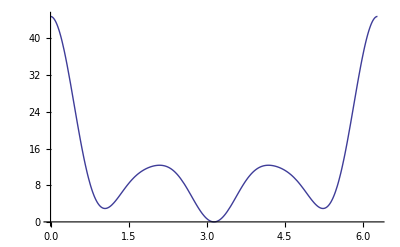

```mathematica
Plot[Erbtest[ϕ],{ϕ,0,2Pi}]
```

```mathematica
The following function is for the dihedral class pairing CT CT CT CT:
```

```mathematica
Erb1[ϕ_]=∑_(n=0)^5 C1[n,1]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C1[0,1]=2.9288;
```

```mathematica
C1[1,1]=-1.4644;
```

```mathematica
C1[2,1]=0.2092;
```

```mathematica
C1[3,1]=-1.67261;
```

```mathematica
C1[4,1]=0;
```

```mathematica
C1[5,1]=0;
```

```mathematica
Erb1[ϕ]
```

2.9288+1.4644 Cos[ϕ]+0.2092 Cos[ϕ]^2+1.67261 Cos[ϕ]^3

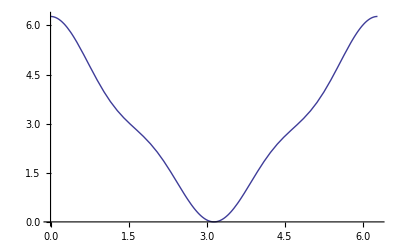

```mathematica
Plot[Erb1[ϕ],{ϕ,0,2Pi}]
```

```mathematica
The following function is for the dihedral class pairing CT CT CT HC:
```

```mathematica
Erb2[ϕ_]=∑_(n=0)^5 C2[n,2]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C2[0,2]=.9665;
```

```mathematica
C2[1,2]=2.89951;
```

```mathematica
C2[2,2]=0;
```

```mathematica
C2[3,2]=-3.86601;
```

```mathematica
C2[4,2]=0;
```

```mathematica
C2[5,2]=0;
```

```mathematica
Erb2[ϕ]
```

0.9665-2.89951 Cos[ϕ]+3.86601 Cos[ϕ]^3

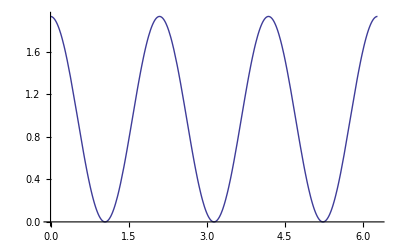

```mathematica
Plot[Erb2[ϕ],{ϕ,0,2Pi}]
```

```mathematica
The following function is for the dihedral class pairing HC CT CT HC.
```

```mathematica
Erb3[ϕ_]=∑_(n=0)^5 C3[n,3]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C3[0,3]=.66525;
```

```mathematica
C3[1,3]=1.99576;
```

```mathematica
C3[2,3]=0;
```

```mathematica
C3[3,3]=-2.66102;
```

```mathematica
C3[4,3]=0;
```

```mathematica
C3[5,3]=0;
```

```mathematica
Erb3[ϕ]
```

0.66525-1.99576 Cos[ϕ]+2.66102 Cos[ϕ]^3

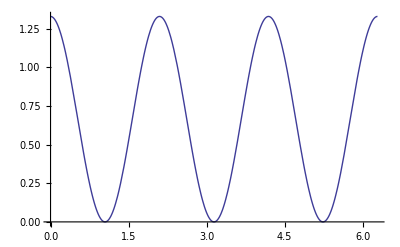

```mathematica
Plot[Erb3[ϕ],{ϕ,0,2Pi}]
```

```mathematica
The following function is for the dihedral class pairing CT CT CT OS:
```

```mathematica
Erb4[ϕ_]=∑_(n=0)^5 C4[n,4]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C4[0,4]=2.87441;
```

```mathematica
C4[1,4]=.58158;
```

```mathematica
C4[2,4]=2.09200;
```

```mathematica
C4[3,4]=-5.54799;
```

```mathematica
C4[4,4]=0;
```

```mathematica
C4[5,4]=0;
```

```mathematica
Erb4[ϕ]
```

2.9288+1.4644 Cos[ϕ]+0.2092 Cos[ϕ]^2+1.6736 Cos[ϕ]^3

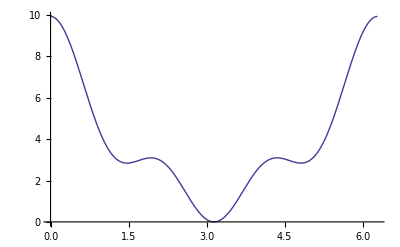

```mathematica
Plot[Erb4[ϕ],{ϕ,0,2Pi}]
```

```mathematica
The following function is for the dihedral class pairing
```

```mathematica
Erb5[ϕ_]=∑_(n=0)^5 C5[n,3]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C5[0,5]=
```

```mathematica
C5[1,5]=
```

```mathematica
C5[2,5]=
```

```mathematica
C5[3,5]=
```

```mathematica
C5[4,5]=
```

```mathematica
C5[5,5]=
```

```mathematica
Erb5[ϕ]
```

```mathematica
Plot[Erb5[ϕ],{ϕ,0,2Pi}]
```

```mathematica
The following function is for the dihedral class pairing
```

```mathematica
Erb6[ϕ_]=∑_(n=0)^5 C6[n,3]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C0[opls182]=
```

```mathematica
C1[opls182]=
```

```mathematica
C2[opls182]=
```

```mathematica
C3[opls182]=
```

```mathematica
C4[opls182]=
```

```mathematica
C5[opls182]=
```

```mathematica
Erb5[ϕ]
```

```mathematica
Plot[Erb5[ϕ],{ϕ,0,2Pi}]
```

```mathematica
The following function is for the dihedral class pairing
```

```mathematica
Erb7[ϕ_]=∑_(n=0)^5 C7[n,3]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C0[opls154]=
```

```mathematica
C1[opls154]=
```

```mathematica
C2[opls154]=
```

```mathematica
C3[opls154]=
```

```mathematica
C4[opls154]=
```

```mathematica
C5[opls154]=
```

```mathematica
The following function is for the dihedral class pairing
```

```mathematica
Erb8[ϕ_]=∑_(n=0)^5 C8[n,3]*(Cos[ϕ-(Pi)])^n;
```

```mathematica
C1[opls155]=
```

```mathematica
C2[opls155]=
```

```mathematica
C3[opls155]=
```

```mathematica
C4[opls155]=
```

```mathematica
C5[opls155]=
```

```mathematica
The following function is for the dihedral class pairing
```

```mathematica
C1[opls157]=
```

```mathematica
C2[opls157]=
```

```mathematica
C3[opls157]=
```

```mathematica
C4[opls157]=
```

```mathematica
C5[opls157]=
```

```mathematica
C1[opls158]=
```

```mathematica
Custom Si Dihedrals
```

```mathematica
Plot[(1-Cos[3r+Pi])+2,{r,0,2*Pi},PlotRange->{0,5},AxesLabel->{Style["ϕ",30],Style["E_Dihedrals",30]},LabelStyle->Directive[0]]
```

```mathematica
Leonardn Jones Potentials
```

```mathematica
LJ potentials for each atom type have parameters Aij and Cij.  It is important to understand the LJ interaction between atoms of each combination.
```

```mathematica
σij[i_,j_]=(1/2)*(σ[i]+σ[j]);
```

```mathematica
ϵ[i_,j_]=Sqrt[ϵ[i]*ϵ[j]];
```

```mathematica
FLJ[i_,j_]=4*ϵ[i,j]*((σij[i,j]/r)^12-(σij[i,j]/r)^6);
```

```mathematica
σ[opls135]=.350;
```

```mathematica
ϵ[opls135]=.276144;
```

```mathematica
σ[opls136]=.350;
```

```mathematica
ϵ[opls136]=.276144;
```

```mathematica
σ[opls137]=.350;
```

```mathematica
ϵ[opls137]=.276144;
```

```mathematica
σ[opls139]=.350;
```

```mathematica
ϵ[opls139]=.276144;
```

```mathematica
σ[opls140]=.350;
```

```mathematica
ϵ[opls140]=.12552;
```

```mathematica
σ[opls154]=.312;
```

```mathematica
ϵ[opls154]=.71128;
```

```mathematica
σ[opls155]=0;
```

```mathematica
ϵ[opls155]=0;
```

```mathematica
σ[opls157]=.350;
```

```mathematica
ϵ[opls157]=.276144;
```

```mathematica
σ[opls158]=.350;
```

```mathematica
ϵ[opls158]=.276144;
```

```mathematica
σ[opls180]=.290;
```

```mathematica
ϵ[opls180]=.58576;
```

```mathematica
σ[opls181]=.350;
```

```mathematica
ϵ[opls181]=.276144;
```

```mathematica
σ[opls182]=.350;
```

```mathematica
ϵ[opls182]=.276144;
```

```mathematica
σ[opls795]=.32150;
```

```mathematica
ϵ[opls795]=.585760;
```

```mathematica
σ[opls796]=0;
```

```mathematica
ϵ[opls796]=0;
```

```mathematica
FLJ[opls135,opls135]
```

1.10458 ((3.37922×10^-6)/r^12-0.00183827/r^6)

```mathematica
FLJ[opls135,opls136]
```

1.10458 ((3.37922×10^-6)/r^12-0.00183827/r^6)

```mathematica
FLJ[opls135,opls137]
```

1.10458 ((3.37922×10^-6)/r^12-0.00183827/r^6)

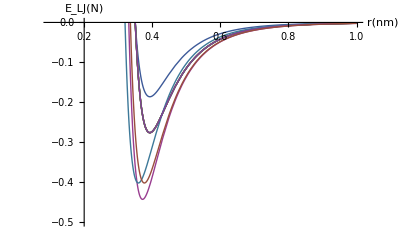

```mathematica
Plot[{FLJ[opls135,opls135],FLJ[opls135,opls136],FLJ[opls135,opls137],FLJ[opls135,opls139],FLJ[opls135,opls140],FLJ[opls135,opls154],FLJ[opls135,opls157],FLJ[opls135,opls158],FLJ[opls135,opls180],FLJ[opls135,opls181],FLJ[opls135,opls795]},{r,.1,1},PlotRange->{-.5,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

```mathematica
Plot[{FLJ[opls136,opls135],FLJ[opls136,opls136],FLJ[opls136,opls137],FLJ[opls136,opls139],FLJ[opls136,opls140],FLJ[opls136,opls154],FLJ[opls136,opls157],FLJ[opls136,opls158],FLJ[opls136,opls180],FLJ[opls136,opls181],FLJ[opls136,opls795]},{r,.1,1},PlotRange->{-.5,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

-Graphics-

```mathematica
Plot[{FLJ[opls137,opls135],FLJ[opls137,opls136],FLJ[opls137,opls137],FLJ[opls137,opls139],FLJ[opls137,opls140],FLJ[opls137,opls154],FLJ[opls137,opls157],FLJ[opls137,opls158],FLJ[opls137,opls180],FLJ[opls137,opls181],FLJ[opls137,opls795]},{r,.1,1},PlotRange->{-.5,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

-Graphics-

```mathematica
Plot[{FLJ[opls139,opls135],FLJ[opls139,opls136],FLJ[opls139,opls137],FLJ[opls139,opls139],FLJ[opls139,opls140],FLJ[opls139,opls154],FLJ[opls139,opls157],FLJ[opls139,opls158],FLJ[opls139,opls180],FLJ[opls139,opls181],FLJ[opls139,opls795]},{r,.1,1},PlotRange->{-.5,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

-Graphics-

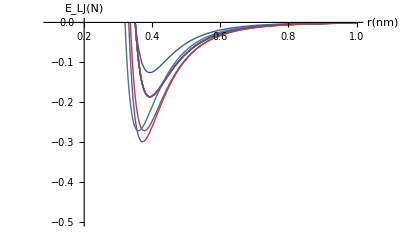

```mathematica
Plot[{FLJ[opls140,opls135],FLJ[opls140,opls136],FLJ[opls140,opls137],FLJ[opls140,opls139],FLJ[opls140,opls140],FLJ[opls140,opls154],FLJ[opls140,opls157],FLJ[opls140,opls158],FLJ[opls140,opls180],FLJ[opls140,opls181],FLJ[opls140,opls795]},{r,.1,1},PlotRange->{-.5,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

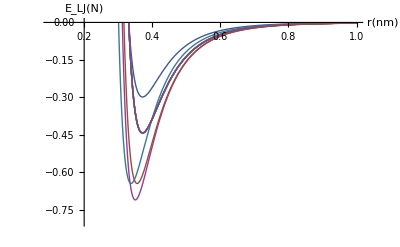

```mathematica
Plot[{FLJ[opls154,opls135],FLJ[opls154,opls136],FLJ[opls154,opls137],FLJ[opls154,opls139],FLJ[opls154,opls140],FLJ[opls154,opls154],FLJ[opls154,opls157],FLJ[opls154,opls158],FLJ[opls154,opls180],FLJ[opls154,opls181],FLJ[opls154,opls795]},{r,.1,1},PlotRange->{-.8,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

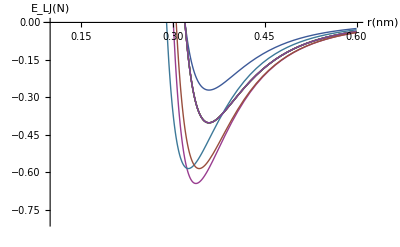

```mathematica
Plot[{FLJ[opls180,opls135],FLJ[opls180,opls136],FLJ[opls180,opls137],FLJ[opls180,opls139],FLJ[opls180,opls140],FLJ[opls180,opls154],FLJ[opls180,opls157],FLJ[opls180,opls158],FLJ[opls180,opls180],FLJ[opls180,opls181],FLJ[opls180,opls795]},{r,.1,.6},PlotRange->{-.8,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

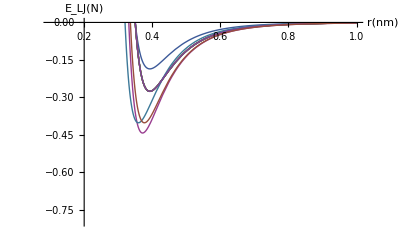

```mathematica
Plot[{FLJ[opls181,opls135],FLJ[opls181,opls136],FLJ[opls181,opls137],FLJ[opls181,opls139],FLJ[opls181,opls140],FLJ[opls181,opls154],FLJ[opls181,opls157],FLJ[opls181,opls158],FLJ[opls181,opls180],FLJ[opls181,opls181],FLJ[opls181,opls795]},{r,.1,1},PlotRange->{-.8,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

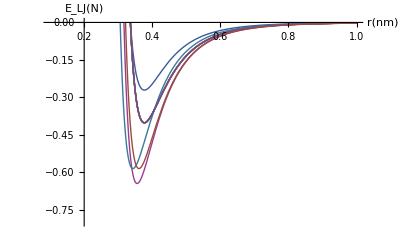

```mathematica
Plot[{FLJ[opls795,opls135],FLJ[opls795,opls136],FLJ[opls795,opls137],FLJ[opls795,opls139],FLJ[opls795,opls140],FLJ[opls795,opls154],FLJ[opls795,opls157],FLJ[opls795,opls158],FLJ[opls795,opls180],FLJ[opls795,opls181],FLJ[opls795,opls795]},{r,.1,1},PlotRange->{-.8,10^-5},AxesLabel->{Style["r(nm)",30],Style["E_LJ(N)",30]},LabelStyle->Directive[20]]
```

```mathematica
Custom Si Dihedrals
```

```mathematica
Coulombic Potentials
```

```mathematica
Coulombic potentials for each atom type have a charge parameter, qi. It is important to consider the interaction of an atom with a unit charge, and then each other atom type to understand the relative strength of different interactions.
```

```mathematica
Fc[a_,b_]=ke*q[a]*q[b]/r^2;
```

```mathematica
q[opls135]=-.18;
```

```mathematica
q[opls136]=-.12;
```

```mathematica
q[opls137]=-.06;
```

```mathematica
q[opls139]=0;
```

```mathematica
q[opls140]=0.06;
```

```mathematica
q[opls154]=-.683;
```

```mathematica
q[opls155]=.418;
```

```mathematica
q[opls157]=.145;
```

```mathematica
q[opls158]=.205;
```

```mathematica
q[opls180]=-.4;
```

```mathematica
q[opls181]=.11;
```

```mathematica
q[opls182]=.14;
```

```mathematica
q[opls235]=.5;
```

```mathematica
q[opls236]=-.5;
```

```mathematica
q[OWspc]=-.8476;
```

```mathematica
q[HWspc]=.4238;
```

```mathematica
Si in PDMS
```

```mathematica
Fc[opls135,opls135,r]
```

(2.91197×10^8)/r^2

```mathematica
Fc[opls135,opls135]
```

(2.91197×10^8)/r^2

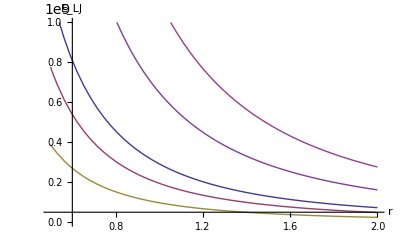

```mathematica
Plot[{Fc[opls135,opls135],Fc[opls135,opls136],Fc[opls135,opls137],Fc[opls135,opls139],Fc[opls135,opls140],Fc[opls135,opls154],Fc[opls135,opls155],Fc[opls135,opls157],Fc[opls135,opls158],Fc[opls135,opls180],Fc[opls135,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

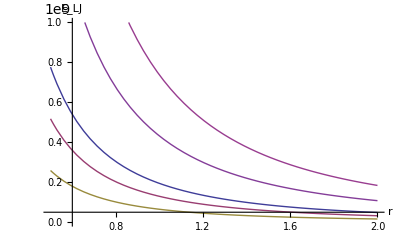

```mathematica
Plot[{Fc[opls136,opls135],Fc[opls136,opls136],Fc[opls136,opls137],Fc[opls136,opls139],Fc[opls136,opls140],Fc[opls136,opls154],Fc[opls136,opls155],Fc[opls136,opls157],Fc[opls136,opls158],Fc[opls136,opls180],Fc[opls136,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

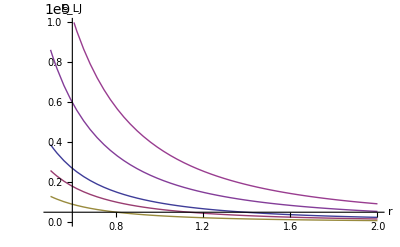

```mathematica
Plot[{Fc[opls137,opls135],Fc[opls137,opls136],Fc[opls137,opls137],Fc[opls137,opls139],Fc[opls137,opls140],Fc[opls137,opls154],Fc[opls137,opls155],Fc[opls137,opls157],Fc[opls137,opls158],Fc[opls137,opls180],Fc[opls137,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

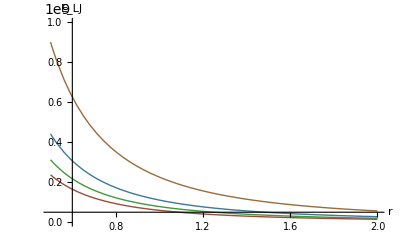

```mathematica
Plot[{Fc[opls140,opls135],Fc[opls140,opls136],Fc[opls140,opls137],Fc[opls140,opls139],Fc[opls139,opls140],Fc[opls140,opls154],Fc[opls140,opls155],Fc[opls140,opls157],Fc[opls140,opls158],Fc[opls140,opls180],Fc[opls140,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

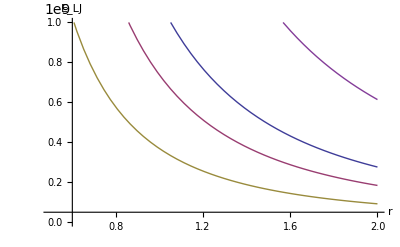

```mathematica
Plot[{Fc[opls154,opls135],Fc[opls154,opls136],Fc[opls154,opls137],Fc[opls154,opls139],Fc[opls139,opls154],Fc[opls154,opls154],Fc[opls154,opls155],Fc[opls154,opls157],Fc[opls154,opls158],Fc[opls154,opls180],Fc[opls154,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

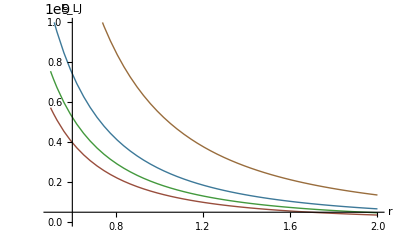

```mathematica
Plot[{Fc[opls157,opls135],Fc[opls157,opls136],Fc[opls157,opls137],Fc[opls157,opls139],Fc[opls139,opls157],Fc[opls157,opls154],Fc[opls157,opls155],Fc[opls157,opls157],Fc[opls157,opls158],Fc[opls157,opls180],Fc[opls157,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

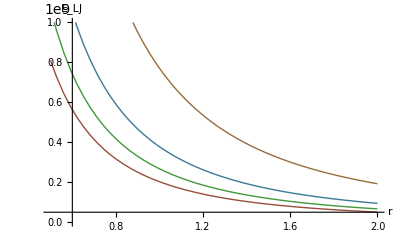

```mathematica
Plot[{Fc[opls158,opls135],Fc[opls158,opls136],Fc[opls158,opls137],Fc[opls158,opls139],Fc[opls139,opls158],Fc[opls158,opls154],Fc[opls158,opls155],Fc[opls158,opls157],Fc[opls158,opls158],Fc[opls158,opls180],Fc[opls158,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

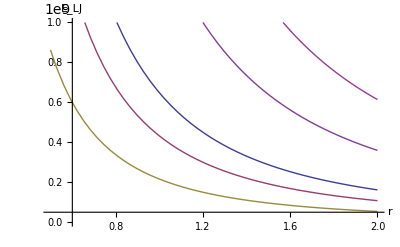

```mathematica
Plot[{Fc[opls180,opls135],Fc[opls180,opls136],Fc[opls180,opls137],Fc[opls180,opls139],Fc[opls139,opls180],Fc[opls180,opls154],Fc[opls180,opls155],Fc[opls180,opls157],Fc[opls180,opls158],Fc[opls180,opls180],Fc[opls180,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

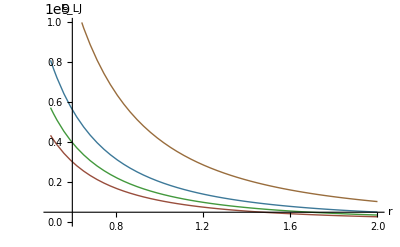

```mathematica
Plot[{Fc[opls181,opls135],Fc[opls181,opls136],Fc[opls181,opls137],Fc[opls181,opls139],Fc[opls139,opls181],Fc[opls181,opls154],Fc[opls181,opls155],Fc[opls181,opls157],Fc[opls181,opls158],Fc[opls181,opls180],Fc[opls181,opls181]},{r,.5,2},PlotRange->{10^6,10^9},AxesLabel->{Style["r",30],Style["E_LJ",30]},LabelStyle->Directive[0]]
```

```mathematica
Plot[{(1/r),(-1/r)},{r,.5,2},PlotRange->{-2,3},AxesLabel->{Style["r",30],Style["E_C",30]},LabelStyle->Directive[0]]
```

```mathematica
Plot[{(1/r),(-1/r)},{r,.5,2},PlotRange->{-2,3},AxesLabel->{Style["r",30],Style["E_C",30]},LabelStyle->Directive[0]]
```

```mathematica
Create a table of the number of atoms of each opls atom type for each polymer.
```